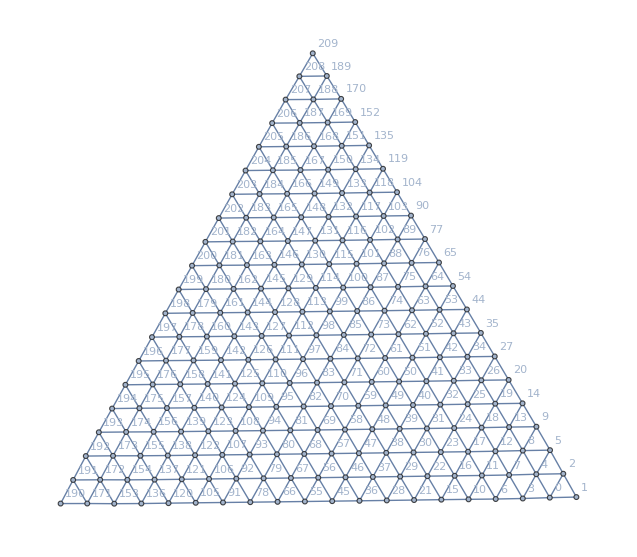

61

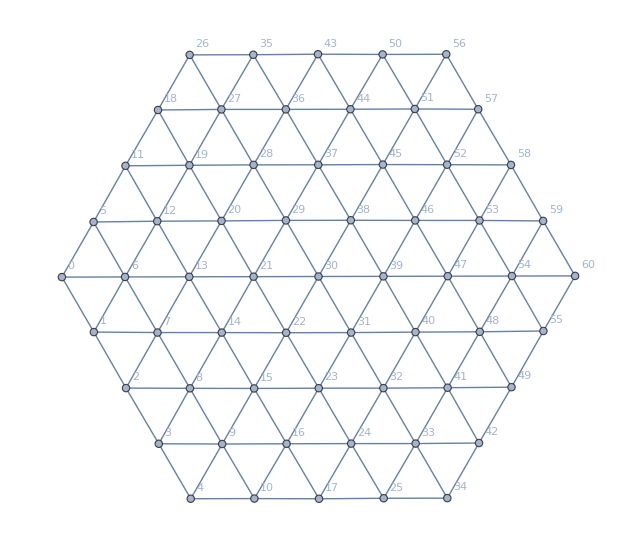

triangularHexagonGridSize11.graphml

```mathematica
G = Import["C:\\Users\\FERMAT\\Documents\\adjMatrix.graphml"];
Graph[G, GraphLayout->"SpringEmbedding", VertexLabels->Automatic]
K= VertexDelete[G, Map[ToString, Join[Join[Range[0,9],Range[90, 209]], {77,89,65,76,88,54,64,75,87,45,55,66,78,79,80,81,67,68,56}]]];
coordinates = Map[(First[#]-> Part[#,2]&),Transpose[{VertexList[K],Range[0, VertexCount[K]-1]}]];
H = VertexReplace[K, coordinates];
VertexCount[H]
Graph[H, VertexLabels->"Name", GraphLayout->"SpringEmbedding"]
Export["triangularHexagonGridSize11.graphml", H]
```